```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/ethans/Documents/Courses/MATH161/Notes/5-DefinitionOfLimit

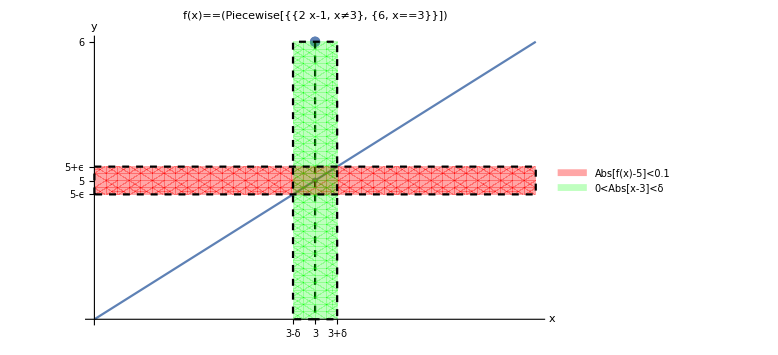

ex1.png

```mathematica
f[x_]=Piecewise[{{2*x-1,x!=3},{6, x==3}}];
x0=3;
l=Limit[f[x],x->x0];
{a,b}={x0-0.5,x0+0.5};
c=Min[f[a],f[b]];
d=Max[f[a],f[b]];
eps=1/10;
modelPlt=Plot[f[x],{x,a,b},AxesLabel->{ x,y},PlotLabel->HoldForm[f[x]]==f[x],ImageSize->Large];
target={x0,l};
targetPnt=Show[
ListPlot[{target},PlotMarkers->"OpenMarkers"],
ListPlot[{{x0,f[x0]}}]
];
specLine=ContourPlot[x==x0,{x,a,b},{y,c,d},ContourStyle->{Black,Dashed}];
xInt=Reduce[Abs[f[x]-l]<eps,x,Reals];
xmin=xInt[[1,1]];
xmax=xInt[[-1,-1]];
del=Min[Abs[x0-xmin],Abs[x0-xmax]];
tolReg=RegionPlot[{Abs[y-l]<eps,Abs[x-x0]<del},{x,a,b},{y,c,d},PlotStyle->{{Red,Opacity[0.35]},{Green,Opacity[0.25]}},BoundaryStyle->{{Black,Dashed}},PlotLegends->{Abs[HoldForm[f[x]]-l]<N[eps],0<Abs[x-x0]<δ}];
plt=Show[
modelPlt,
targetPnt,
specLine,
tolReg,
PlotRange->All,
Ticks->{{{x0-del,StringForm["``-δ",x0]},x0,{x0+del,StringForm["``+δ",x0]}},{{l-eps,StringForm["``-ϵ",l]},l,{l+eps,StringForm["``+ϵ",l]},f[x0]}}
]
Export["ex1.png",plt]
```

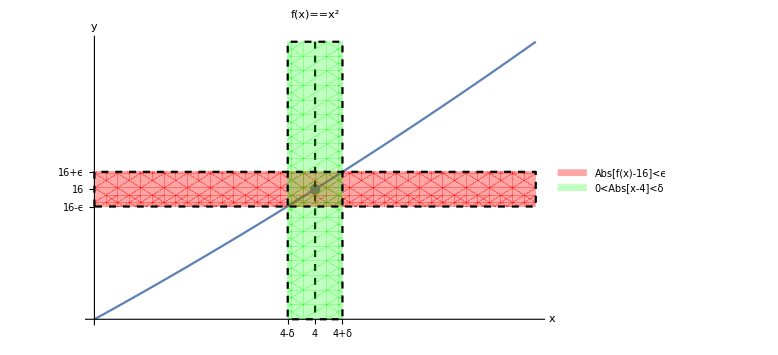

```mathematica
f[x_]=x^2;
x0=4;
l=Limit[f[x],x->x0];
{a,b}={x0-0.5,x0+0.5};
c=Min[f[a],f[b]];
d=Max[f[a],f[b]];
eps=5/10;
modelPlt=Plot[f[x],{x,a,b},AxesLabel->{ x,y},PlotLabel->HoldForm[f[x]]==f[x],ImageSize->Large];
target={x0,l};
targetPnt=Show[
ListPlot[{target},PlotMarkers->"OpenMarkers"],
ListPlot[{{x0,f[x0]}}]
];
specLine=ContourPlot[x==x0,{x,a,b},{y,c,d},ContourStyle->{Black,Dashed}];
xInt=Reduce[Abs[f[x]-l]<eps,x,Reals];
xmin=xInt[[1,1]];
xmax=xInt[[-1,-1]];
del=Min[Abs[x0-xmin],Abs[x0-xmax]];
tolReg=RegionPlot[{Abs[y-l]<eps,Abs[x-x0]<del},{x,a,b},{y,c,d},PlotStyle->{{Red,Opacity[0.35]},{Green,Opacity[0.25]}},BoundaryStyle->{{Black,Dashed}},PlotLegends->{Abs[HoldForm[f[x]]-l]<ϵ,0<Abs[x-x0]<δ}];
plt=Show[
modelPlt,
targetPnt,
specLine,
tolReg,
PlotRange->All,
Ticks->{{{x0-del,StringForm["``-δ",x0]},x0,{x0+del,StringForm["``+δ",x0]}},{{l-eps,StringForm["``-ϵ",l]},l,{l+eps,StringForm["``+ϵ",l]}}}
]
(*Export["ex2.png",plt]*)
```